# Autoevaluación I. Análisis de sistemas de dos electrones

1. Analiza los datos de la tabla 1.3 (página 25 de los apuntes disponibles en Moodle). Dicha tabla recoge distintos sistemas con dos electrones, junto con diferentes valores de energía del estado fundamental.
	(a) .08Añadir una nueva columna a la tabla que recoja los valores de la energía del estado fundamental usando el modelo de partícula independiente junto al apantallamiento de los electrones.
	(b) Representar gráficamente, para cada sistema, los valores de la energía obtenidos con los métodos de partícula independiente, perturbativo, variacional sencillo y el valor exacto indicados en la tabla. .08Añade también la nueva columna.
	(c) Calcular y representar la diferencia relativa de cada método respecto al valor exacto proporcionado.
	(d) Hacer un análisis comparativo de los resultados obtenidos, indicando el método que mejores resultados proporcione, impacto del término repulsivo en función de , posibles mejoras, etc. 

(a)
En el modelo de partícula independiente, tenemos el Hamiltoniano sin perturbar siguiente,

						

Si añadimos apantallamiento, introducimos un potencial  central, que debemos elegir de forma que el efecto de la perturbación  sobre los niveles sin perturbar sea pequeño. 

Sabemos que el efecto neto de un electrón sobre el otro es el de apantallar la carga del núcleo. Por tanto, una elección sencilla y conveniente de tomar el potencial central será

						
												
donde  es un parámetro denominado constante de apantallamiento y  es la carga efectiva que siente cada electrón resultante de la carga nuclear y el efecto de apantallamiento de carga, inducido por el otro electrón. Supondremos que .

Como el potencial es tipo culombiano, la expresión de las energías monoparticulares será la misma que el caso sin apantallamiento, pero sustituyendo  por , tal que

						

Luego, la energía del estado fundamental será,

					
										
A continuación vamos a escribir un código para calcular esta energía.

```mathematica
Z = {1, 2, 3, 4, 5, 6};
E0 = -(Z-0.30)^2;
Print["Los valores de la energía con apantallamiento son: ", E0]
```

Los valores de la energía con apantallamiento son: {-0.49,-2.89,-7.29,-13.69,-22.09,-32.49}

Luego, tendremos la tabla 1.3 con la nueva columna como:


 | Part. indep | Apantallamiento | Perturbativo | Variacional | Exacto
 | -1 | -0.49 | -0.375 | -0.473 | -0.528
He | -4 | -2.89 | -2.75 | -2.848 | -2.904
 | -9 | -7.29 | -7.125 | -7.222 | -7.28
 | -16 | -13.69 | -13.5 | -13.6 | -13.66
 | -25 | -22.09 | -21.88 | -21.97 | -22.03
 | -36 | -32.49 | -32.25 | -32.35 | -32.41	

Tabla 1: Tabla 1.3 de los apuntes de Moodle con la columna de la energía de partícula independiente junto al apantallamiento añadida y calculada anteriormente.

(b)

Vamos a crear ahora el código para representar gráficamente los valores de energía de la Tabla 1.

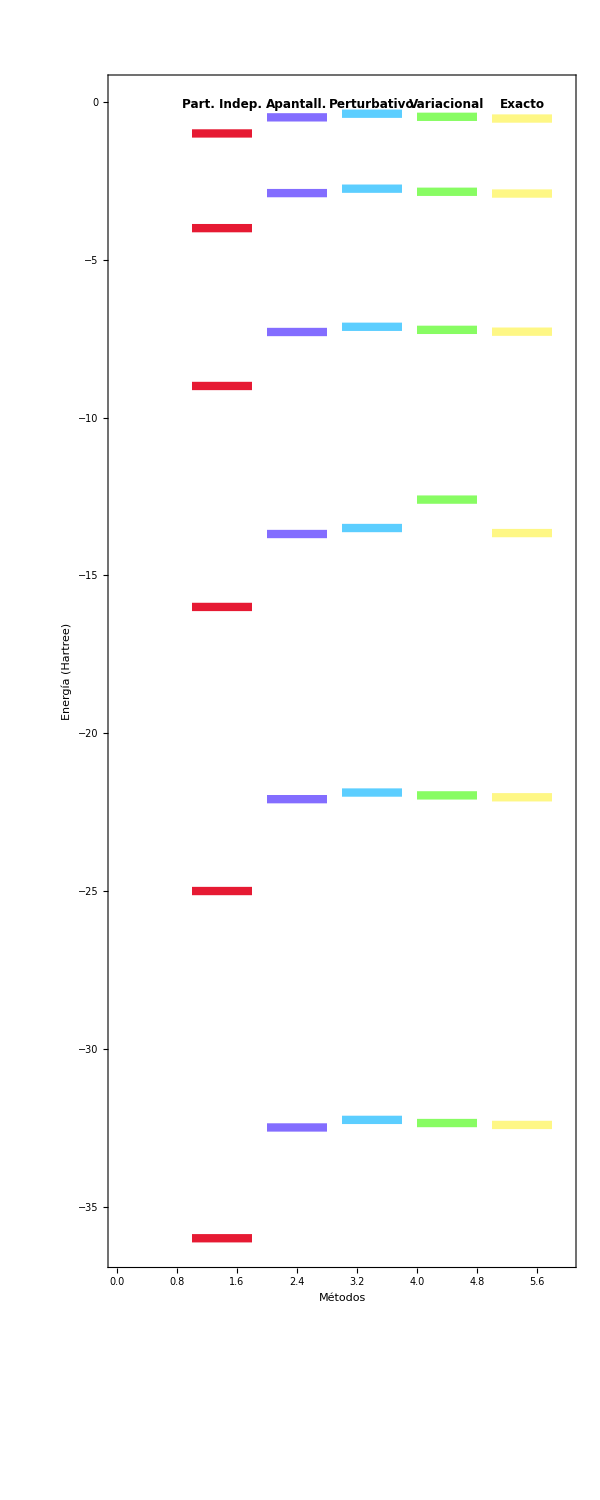

```mathematica
energias={{-1, -4, -9, -16, -25, -36},(*Método 1*)
{-0.49, -2.89, -7.29, -13.69, -22.09, -32.49},(*Método 2*)
{-0.375, -2.75, -7.125, -13.5, -21.88, -32.25},(*Método 3*)
{-0.473, -2.848, -7.222, -12.6, -21.97, -32.35},(*Método 4*)
{-0.528, -2.904, -7.28, -13.66, -22.03, -32.41}    (*Método 5*)};

nombresMetodos={"Part. Indep.","Apantall.","Perturbativo","Variacional","Exacto"};

(*Generar colores automáticamente según el número de métodos*)
numMetodos=Length[energias];
colores=ColorData["BrightBands"][#]&/@Subdivide[numMetodos];

(*Crea la gráfica*)
grafica=Graphics[{Table[{colores[[i]],Thickness[0.01],Line[{{i,#},{i+0.8,#}}]&/@energias[[i]]},{i,numMetodos}],
Table[Text[Style[nombresMetodos[[i]],12,Bold],{i+0.4,Max[Flatten[energias]]+0.3}],{i,numMetodos}]},
PlotRange->{{0,numMetodos+1},{Min[Flatten[energias]]-0.2,Max[Flatten[energias]]+0.5}},
Frame->True,FrameLabel->{"Métodos","Energía (Hartree)"},ImageSize->600]
```

En este espectro de energías hemos representado los valores de la Tabla 1 en el mismo gráfico, para ver las diferencias de forma más clara. 

(c)

Ahora vamos a presentar el código para calcular la diferencia relativa de cada método respecto al valor exacto de la energía. Usaremos la fórmula de la diferencia relativa siguiente,

```mathematica
(* Sistemas atómicos dielectrónicos *)
atomos = {"H⁻", "He", "Li⁺", "Be.b2⁺", "B.b3⁺", "C⁴⁺"};
(* Valor exacto de la energía del estado fundamental para los diferentes átomos *)
valorExacto = {-0.528, -2.904, -7.28, -13.66, -22.03, -32.41};
(* Energías calculadas con diferentes métodos *)
energias = {
   {"Part. Indep.", {-1, -4, -9, -16, -25, -36}},
   {"Apantall.", {-0.49, -2.89, -7.29, -13.69, -22.09, -32.49}}, 
   {"Perturbativo", {-0.375, -2.75, -7.125, -13.5, -21.88, -32.25}},
   {"Variacional", {-0.473, -2.848, -7.222, -13.6, -21.97, -32.35}}
};

(* Calcular diferencias relativas porcentuales *)
diferenciasRelativas = Table[
   {metodos[[1]], 100 * Abs[(metodos[[2]] - valorExacto)/valorExacto]},
   {metodos, energias}
];
```

Ahora representamos los valores obtenidos en una tabla.

```mathematica
(* Tabla con colorines *)
tablaProfesional = Table[
   metodo = diferenciasRelativas[[i, 1]];
   errores = diferenciasRelativas[[i, 2]];
   
   Join[
    {Style[metodo, FontWeight -> Bold, Black]},
    Table[
     Style[NumberForm[errores[[j]], {4, 1}], 11, 
      FontColor -> Which[
        errores[[j]] < 1, Green,    (* Verde: excelente *)
        errores[[j]] < 5, Yellow,      (* Amarillo: decente *)
        errores[[j]] < 15, Orange,  (* Naranja: regular *)
        True, Red                 (* Rojo: fatal *)
      ]],
     {j, Length[errores]}]
   ],
   {i, Length[diferenciasRelativas]}
 ];

Grid[
 Prepend[tablaProfesional, 
  Prepend[Map[Style[#, Bold, White] &, atomos], 
   Style["Método", Bold, White, FontSize -> 12]]],
 Frame -> All,
 Alignment -> Center,
 Background -> {None, {Black, {RGBColor[0.55, 0.55, 0.45]}}},
 ItemSize -> {All, 1.4},
 Dividers -> All,
 FrameStyle -> GrayLevel[0.3],
 ImageSize -> 800
]
```

Método | H⁻ | He | Li⁺ | Be.b2⁺ | B.b3⁺ | C⁴⁺
Part. Indep. | 89.4 | 37.7 | 23.6 | 17.1 | 13.5 | 11.1
Apantall. | 7.2 | 0.5 | 0.1 | 0.2 | 0.3 | 0.2
Perturbativo | 29.0 | 5.3 | 2.1 | 1.2 | 0.7 | 0.5
Variacional | 10.4 | 1.9 | 0.8 | 0.4 | 0.3 | 0.2

Tabla 2: Esta tabla representa los valores de los errores relativos de cada método respecto al valor exacto, con cada átomo. El color verde representa que el error es excelente, el naranja representa que es decente, el amarillo que es mejorable y el rojo que es horrible. 

Ahora vamos a escribir el código para representar estos errores relativos .

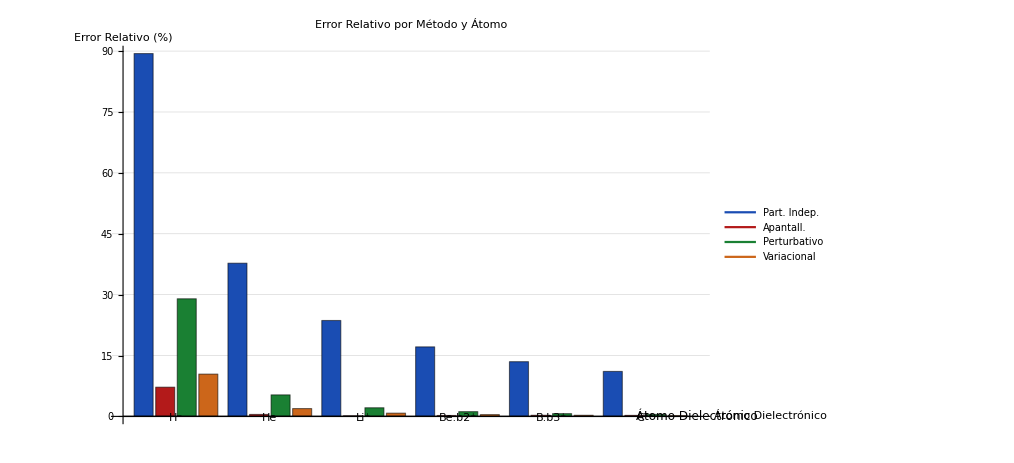

```mathematica
(* Gráfico con leyenda usando Legended - compatible *)
graficoProfesional = Legended[
  BarChart[
    diferenciasRelativas[[All, 2]] // Transpose,
    ChartLabels -> {
      Placed[atomos, Axis],
      None
    },
    ChartLayout -> "Grouped",
    ChartStyle -> {
      RGBColor[0.1, 0.3, 0.7],   (* Azul oscuro *)
      RGBColor[0.7, 0.1, 0.1],   (* Rojo oscuro *)
      RGBColor[0.1, 0.5, 0.2],   (* Verde oscuro *)
      RGBColor[0.8, 0.4, 0.1]    (* Naranja oscuro *)
    },
    PlotLabel -> Style["Error Relativo por Método y Átomo", 
      FontFamily -> "Times", 14, Bold],
    AxesLabel -> {
      Style["Átomo Dielectrónico", FontFamily -> "Times", 12],
      Style["Error Relativo (%)", FontFamily -> "Times", 12]
    },
    GridLines -> {None, Automatic},
    GridLinesStyle -> Directive[GrayLevel[0.8], Dashed],
    ImageSize -> 750,
    BaseStyle -> {FontFamily -> "Times", FontSize -> 10}
  ],
  Placed[
    LineLegend[
      {RGBColor[0.1, 0.3, 0.7], RGBColor[0.7, 0.1, 0.1], 
       RGBColor[0.1, 0.5, 0.2], RGBColor[0.8, 0.4, 0.1]},
      energias[[All, 1]],
      LegendLayout -> "Column",
      LabelStyle -> {FontFamily -> "Times", FontSize -> 10}
    ],
    {{0.85, 0.85}}
  ]
]
```

(d)

Observamos que:

El método de partícula independiente es el que más discrepa de todos, cosa que tiene sentido, pues es la aproximación más ‘brusca’ que hacemos, pues tratamos a los electrones como partículas libres, pero sabemos que no podemos hacer esto porque la interacción de Coulomb siempre está presente entre cargas, ya que es una fuerza de alcance infinito (además de otros fenómenos cuánticos).

El método de partícula independiente con apantallamiento vemos que también difiere del valor exacto, pero quitando el , es el método que más se aproxima de todos. Cosa que puede sorprender, pero también es lógico, pues el valor de apantallamiento de  es un valor semiempírico que funciona muy bien, como hemos podido observar. Para el  no funciona bien, debido a que este sistema es débilmente ligado y la constante  es demasiado grande para un .

El método perturbativo tiene un error tan grande con , debido a que la perturbación es demasiado grande, pues
						
mientras que . Por tanto, la perturbación es del mismo orden que el Hamiltoniano no perturbado, por lo que no se cumple que . Para el resto de átomos seguimos teniendo error relativo mejorable, pero se debe a lo anterior, pues vemos que cuanto más grande sea el átomo, menos error relativo tenemos, cosa que se debe a que la perturbación es cada vez más pequeña, por lo que la aproximación es más precisa.

El método variacional tiene un error relativo bajo, debido a que el propio método optimiza automáticamente los parámetros, pues establece una cota superior de la energía,
						
que se cumple siempre.

Para obtener valores muy precisos de la energía se emplea el método variacional de Rayleigh-Ritz, pues converge más rápido que otras propuestas que existen de métodos variational. Este método consiste en construir una nueva función de onda prueba, denominada función de onda prueba de Hylleras. Para ello, sabemos que el estado fundamental tiene , por lo que la función de onda solo dependerá de ,  y . Hacemos el cambio de variable seiguiente,
				, ;	, ; 	, 
Así, la función de onda prueba de Hylleras queda como,
					
donde los coeficientes  son parámetros variacionales lineales y  es un parámetro variacional no lineal, similar a la carga efectiva  empleada anteriormente. Como la función de onda es espacialmente simétrica, la potencia de  debe ser par. El número  determina el número de sumandos.

Notemos que el caso  reduce la función de onda prueba a
						
con  en este caso.

Otro método más sencillo para obtener una buena aproximación es jugar con la constante de apantallamiento, pero estableciendo una constante de apantallamiento  para cada . Sabemos que  Por tanto, si usamos los valores exactos de la energía, podremos determinar con exactitud la constante de apantallamiento. Veamos el código,

```mathematica
Z = {1, 2, 3, 4, 5, 6};
valorExacto = {-0.528, -2.904, -7.28, -13.66, -22.03, -32.41};
S = Z - Sqrt[-valoresExactos];
Print["Los valores exactos de la constante de apantallamiento son: ", S]
Print["Podemos calcular la energía exacta usando estas constantes."]
Print["Para ello, usamos la energía de partícula independiente + apantallamiento."]
ES = -(Z-S)^2;
Print["Asi, el valor exacto de las energías son: ", ES]
Print["Vemos que coinciden con los valores de energía exactos: ", valorExacto]
```

Los valores exactos de la constante de apantallamiento son: {1-√-valoresExactos,2-√-valoresExactos,3-√-valoresExactos,4-√-valoresExactos,5-√-valoresExactos,6-√-valoresExactos}

Podemos calcular la energía exacta usando estas constantes.

Para ello, usamos la energía de partícula independiente + apantallamiento.

Asi, el valor exacto de las energías son: {valoresExactos,valoresExactos,valoresExactos,valoresExactos,valoresExactos,valoresExactos}

Vemos que coinciden con los valores de energía exactos: {-0.528,-2.904,-7.28,-13.66,-22.03,-32.41}

Este último método ‘hace trampa’ pues hace uso de la energía exacta de los átomos. Aunque alomejor existe alguna función que cuadre con  y podamos encontrar una función exacta para obtener las energías de los átomos dielectrónicos.